#### Text copied from the paper:

```mathematica
text =
"acetic acid, benzaldehyde, 2,3-butanedione, butanol, decanal, 2,3-dihydrofuran, 2-ethylhexanol, furfural, hexadecane, hexanal, methoxyphenyloxime, nonanal, octanal, pentanal, and undecane";
```

```mathematica
display=Column[Map[Row,#~Riffle~{"\t"," "}&/@#],Spacings->1]&;

data=Block[{list,info,modify,missing,ch},
modify={
"methoxyphenyloxime"->"oxime-, methoxy-phenyl-_",
"ethylhexanol" -> "ethyl-1-hexanol",
"and "->""};
list=text~StringSplit~ ", "~StringReplace~modify~Capitalize~ "AllWords"~
StringDelete~{" ", "-"};
info=Outer[ChemicalData,list,{"Name",None,"Formula"}]//Quiet;
missing=First/@Position[info,ChemicalData]//Union;
If[AnyTrue[list[[missing]],#~StringContainsQ~"Methoxy"&],
modify[[1,1]]="Name";
ch=ServiceExecute["PubChem",#,First@modify]&,Return[]];
info[[First@missing]]=
Normal@ch["CompoundProperties"][1,{"IUPACName",Head,"MolecularFormula"}]/.
Association->Show[ch["CompoundSDF"]["StructureDiagram",1],ImageSize->Small];
info];
```

For more info on missing fields → "PubChem Reference"paclet:ref/service/PubChem

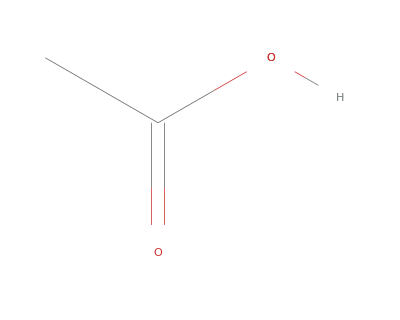
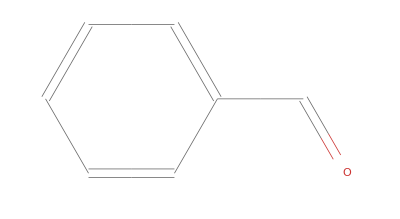
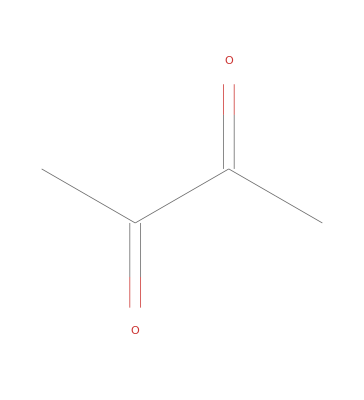
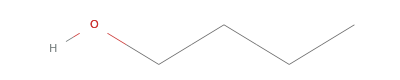
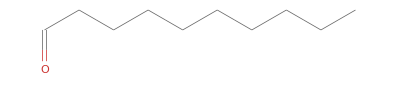
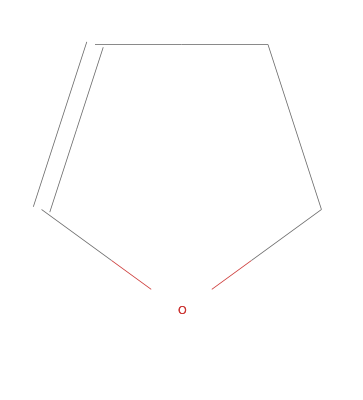
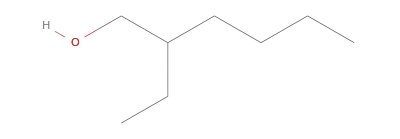
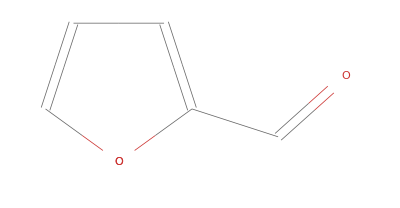
acetic acid	-Graphics- CH_3CO_2H
benzaldehyde	-Graphics- C_6H_5CHO
diacetyl	-Graphics- CH_3COCOCH_3
1-butanol	-Graphics- CH_3(CH_2)_3OH
decanal	-Graphics- CH_3(CH_2)_8CHO
2,3-dihydrofuran	-Graphics- C_4H_6O
2-ethylhexanol	-Graphics- CH_3(CH_2)_3CH(C_2H_5)CH_2OH
furfural	-Graphics- C_5H_4O_2
N-hexadecane	-Graphics- CH_3(CH_2)_14CH_3
caproic aldehyde	-Graphics- CH_3(CH_2)_4CHO
methyl (Z)-N-hydroxybenzenecarboximidate	-Graphics- C8H9NO2
nonanal	-Graphics- CH_3(CH_2)_7CHO
octanal	-Graphics- CH_3(CH_2)_6CHO
valeraldehyde	-Graphics- CH_3(CH_2)_3CHO
undecane	-Graphics- CH_3(CH_2)_9CH_3

```mathematica
display[data]
```

#### A little bit of image processing

```mathematica
Block[{show,img,save=Export[ToString@First[#2]<>".png",#1]&},
show=display/@Partition[data,UpTo@Ceiling[Length@data/2]];
img=Import/@MapIndexed[save,show];
MapIndexed[save,
ImageCrop[#,Ceiling[Max/@Transpose[ImageDimensions/@img],20],
Padding->White]&/@img];
Directory[]]
```

#### Playing with "PubChem Reference"paclet:ref/service/PubChem

```mathematica
ServiceExecute["PubChem","CompoundDescription","Name"->"methyl (Z)-N-hydroxybenzenecarboximidate"]
```

```mathematica
ServiceExecute["PubChem","CompoundSynonyms","CompoundID"->9602988]
```

```mathematica
ServiceExecute["PubChem","CompoundSDF","CompoundID"->9602988]["Graphics3D",1]
```

-Graphics3D-

WolframAlphaQueryResults

molar mass | 151.2 g/mol
formula | C_8H_9NO_2

```mathematica
ChemicalData[LinguisticAssistant]
```

ChemicalData::notent: Molecule[{"C", "O", "C", "N", "O", "C", "C", "C", "C", "C", "C", "H", "H", "H", "H", "H", "H", "H", "H", "H"}, {Bond[{1, 2}, "Single"], Bond[{2, 3}, "Single"], Bond[{3, 4}, "Double"], Bond[{4, 5}, "Single"],…, Bond[{1, 13}, "Single"], Bond[{1, 14}, "Single"], Bond[{5, 15}, "Single"], Bond[{7, 16}, "Single"], Bond[{8, 17}, "Single"], Bond[{9, 18}, "Single"], Bond[{10, 19}, "Single"], Bond[{11, 20}, "Single"]}, {}] is not a known entity, class, or tag for ChemicalData. Use ChemicalData[] for a list of entities.

ChemicalData[Molecule[…]]